## Alpha-Spektroskopie

### Imports

```mathematica
Filenames = {"AIR", "AMSPKTR","CALIBR"};
Filepaths=NotebookDirectory[]<>"..\\data\\"<>#1&/@Filenames;

rawData = Import[#1<>".DAT","List"] &/@Filepaths ;
kalibrData = rawData[[3]];
airData=rawData[[1]];
sptrData=rawData[[2]];

CustomParameterTable[fits_,digits_]:=Module[{parameters,parameterTableValues,rows,tableData},
parameters= ToString[#1[[1]],StandardForm]&/@(fits["BestFitParameters"]);
parameterTableValues={ScientificForm[#1[[1]],digits],ScientificForm[#1[[2]],digits]}&/@fits["ParameterTableEntries"];
parameterTableValues=ToString[#1,StandardForm]&/@#1&/@parameterTableValues;
rows=MapThread[Flatten[{#1,#2}]&,{parameters,parameterTableValues}];
tableData=Join[{{"","Wert","Standardabweichung"}},rows];
Style[Grid[tableData,
Alignment->{Left,Automatic},Dividers->{{2->GrayLevel[0.7]},{2->GrayLevel[0.7]}},Spacings->{{2->1},{2->0.75}}],"DialogStyle"]
]
```

### Energie-Kalibration

{{33.6787,2743/5,24687/100,0.128487},{138.253,5486/5,5486/25,0.113263},{452.902,2743,2743/20,0.129501},{968.743,5486,1,0.0495681}}

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.29403 | 0.0117396 | 450.953 | 4.91738×10^-6
b | 357.446 | 11.3722 | 31.4314 | 0.00101068

| Wert | Standardabweichung
a | 5.294 | 1.174
b | 3.574 | 1.137

| Wert | Standardabweichung
μ | 3.368 | 1.285
σ | 1.303 | 1.285
k | 2.291 | 1.956 |  | Wert | Standardabweichung
μ | 1.383 | 1.133
σ | 1.274 | 1.133
k | 2.465 | 1.898
 | Wert | Standardabweichung
μ | 4.529 | 1.295
σ | 1.27 | 1.295
k | 2.197 | 1.941 |  | Wert | Standardabweichung
μ | 9.687 | 4.957
σ | 1.065 | 4.957
k | 3.485 | 1.404

{7011.605764712136/E^(0.29434965581444056*(-33.67872074878762 + x)^2),7717.455825318301/E^(0.30789071693589276*(-138.25335222258695 + x)^2),6904.329823546912/E^(0.31021660410784563*(-452.90210260199433 + x)^2),13050.635733856781/E^(0.4405445287921415*(-968.7432082800937 + x)^2)}

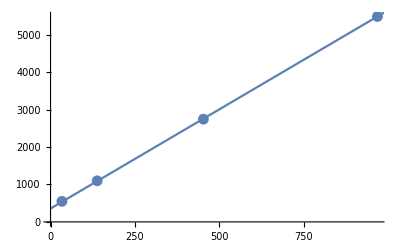

```mathematica
kalibrDampening={10,5,2,1};
kalibrPeakPositions={34,138,452,968};
model[x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));


kalibrFits=NonlinearModelFit[kalibrData, model[x], {{μ, #1}, {σ, 2}, {k, 8000}}, x]&/@kalibrPeakPositions;

kalibrParameters=#1[[1,1]]&/@(#1[[{1,2}]]&/@#1["ParameterTableEntries"]&/@kalibrFits);

kalibrParameters=MapThread[{#1,#2}&,{kalibrParameters,5486/#1&/@kalibrDampening}];
kalibrParametersLatex=MapThread[Join[#1,{Max[(#1[[2]])/20*(#2-1),1]}]&,{kalibrParameters,kalibrDampening}];
kalibrParametersLatex=MapThread[Join[#1,{#2}]&,{kalibrParametersLatex,#1["ParameterErrors"][[1]]&/@kalibrFits}]

errors=kalibrParametersLatex[[All,3]];
kalibrFunction=NonlinearModelFit[kalibrParameters,a x+b,{a,b},{x},Weights->1/errors^2];
kalibrFunction["ParameterTable"]
kalibrFunction["CorrelationMatrix"];
kalibrFitFunctions=Normal/@kalibrFits;

bands95[x_]= nlm["SinglePredictionBands",ConfidenceLevel->0.95];
Export[Filepaths[[3]] <>"-fitted.DAT", N[kalibrParametersLatex], "Table"];

CustomParameterTable[kalibrFunction,4]

Grid[{{CustomParameterTable[kalibrFits[[1]],4],
CustomParameterTable[kalibrFits[[2]],4]},
{CustomParameterTable[kalibrFits[[3]],4],
CustomParameterTable[kalibrFits[[4]],4]}}]


Format[#1,InputForm]&/@kalibrFitFunctions

Format[Normal[kalibrFunction],InputForm];
Format[bands95[x],InputForm];
Show[ListPlot[kalibrParameters],Plot[{Normal[kalibrFunction],bands95[x]},{x,0,1000}]]
```

### Alpha-Peaks von Amerikanum

a_1 e^{b_1 x}+a_2 e^{b_2 x}+a_3 e^{b_3 x}+\frac{k_1 e^{-\frac{\left(x-\mu _1\right){}^2}{2 \sigma _1^2}}}{\sqrt{2 \pi } \sigma _1}+\frac{k_2 e^{-\frac{\left(x-\mu _2\right){}^2}{2 \sigma _2^2}}}{\sqrt{2 \pi } \sigma _2}+\frac{k_3 e^{-\frac{\left(x-\mu _3\right){}^2}{2 \sigma _3^2}}}{\sqrt{2 \pi } \sigma _3}+\frac{k_4 e^{-\frac{\left(x-\mu _4\right){}^2}{2 \sigma _4^2}}}{\sqrt{2 \pi } \sigma _4}

| Wert | Standardabweichung
μ_1 | 5.486 | 4.063
σ_1 | 9.847 | 4.442
k_1 | 5.73 | 2.329
μ_2 | 5.448 | 2.877
σ_2 | 1.305 | 3.302
k_2 | 1.213 | 2.514
μ_3 | 5.393 | 2.016
σ_3 | 1.232 | 2.082
k_3 | 1.291 | 1.854
μ_4 | 5.529 | 3.572
σ_4 | -1.111 | 3.773
k_4 | -6.359 | 1.81

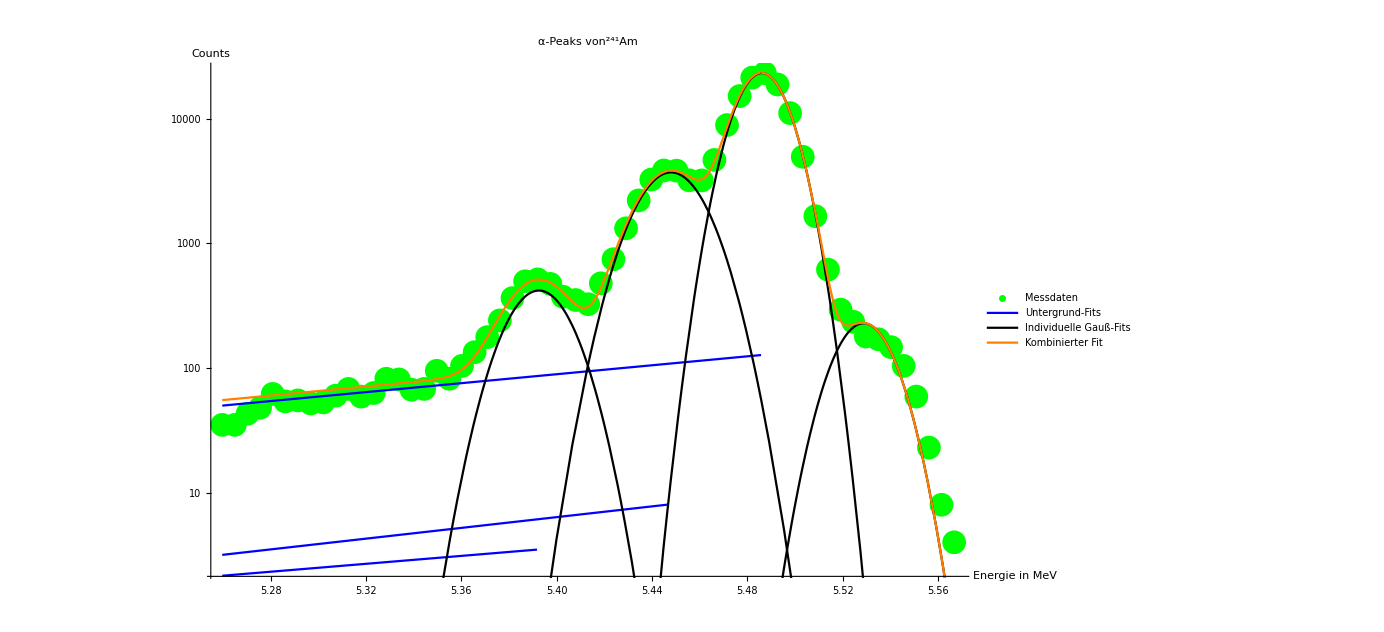

-Graphics-

```mathematica
(*Offset als variable, damit der bereich vor den eigentlichen peaks leichter verkleinert/vergrößert werden kann *)
offset=14;
relevantSptrData=Take[MapIndexed[{(Normal[kalibrFunction]/.x->First[#2])/1000,#1}&,sptrData],{940-offset,985}];
(*Models for the gaussian and background fits*)
gaussModel[μ_,σ_,k_,x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));

model2[x_] =a*Exp[b x];
model3[a_,b_,x_] =a*Exp[b x];

(*Intervals of relevant data for the gaussian fits*)
intervals={{8,14},{17,24},{26,36},{37,43}} + offset;


Module[{bgFitsComplete,fits,bgFits,gaussFits,sortedIntervals,currentInterval,data,noBgData,noGaussData,peakOrder,backgroundFit,gaussFit,i,n,cutoff,piecewise,sumGaussParameters,sumGaussParameterGuesses,sumGaussModel,spktrPeakFitsRefined,cutoffN},
data=relevantSptrData;
bgFitsComplete=bgFits=gaussFits={};
peakOrder={3,2,1,4};
For[i=1,i≤4,i++,
n=peakOrder[[i]];
(*Fit exponential functionto background, so we can remove it from our further calcualtions*)
backgroundFit=Quiet@NonlinearModelFit[Take[data,5+offset], model2[x], {a, b}, x];
(*Define background function until the peak*)

(*Interval relevant to the current peak*)
currentInterval = Take[data,{intervals[[n,1]],intervals[[n,2]]}];
(*Fit gaussian to current peak*)
gaussFit=NonlinearModelFit[currentInterval, model[x], {{μ, Mean[currentInterval[[All,1]]]}, {σ, 1.86}, {k,Mean[currentInterval[[All,2]]]}}, x];
cutoff=gaussFit["BestFitParameters"][[1,2]];
piecewise=Piecewise[{{backgroundFit["BestFit"],x<cutoff},{0,x>cutoff+1}}];
(*Subtrat background from data up to the relevant peak, make sure values stay at 0 or above*)
noBgData={#1[[1]],#1[[2]]-piecewise/.x->#1[[1]]}&/@data;
noBgData={#1[[1]],Max[#1[[2]],0]}&/@noBgData;

(*Subtract Gaussian from data*)
noGaussData={#1[[1]],#1[[2]]-gaussFit["BestFit"]/.x->#1[[1]]}&/@noBgData;
noGaussData={#1[[1]],Max[#1[[2]],0]}&/@noGaussData;
bgFitsComplete=Append[bgFitsComplete,backgroundFit];
bgFits=Append[bgFits,piecewise];
gaussFits=Append[gaussFits,gaussFit];
fits=Join[bgFits,gaussFits];

Show[
ListLogPlot[data,PlotRange->All,PlotStyle->Green],
ListLogPlot[noBgData,PlotRange->All,PlotStyle->Blue],
ListLogPlot[noGaussData,PlotRange->All,PlotStyle->Orange],
LogPlot[piecewise,{x,First[data][[1]],Last[data][[1]]},PlotStyle->Orange],
LogPlot[gaussFit["BestFit"],{x,First[data][[1]],Last[data][[1]]},PlotStyle->Black]
];
data=noGaussData;
];
extBgFitsComplete=Take[bgFitsComplete,3];
fits=Normal[#1]&/@fits;

sumGaussParameters={Subscript[μ, #1],Subscript[σ, #1],Subscript[k, #1]}&/@Range[1,4];
sumGaussParameterGuesses=MapThread[{#1,#2[[All,2]]}&,{sumGaussParameters,#1["BestFitParameters"]&/@gaussFits}];
sumGaussParameterGuesses=Flatten[sumGaussParameterGuesses=Transpose[#1]&/@sumGaussParameterGuesses,1];
sumGaussModel[x_]=Total[gaussModel[#1[[1]],#1[[2]],#1[[3]],x]&/@sumGaussParameters]+Take[Total[bgFits],3];

Print[TeXForm[Total[gaussModel[#1[[1]],#1[[2]],#1[[3]],x]&/@sumGaussParameters]+Total[model3[#1[[1]],#1[[2]],x]&/@({Subscript[a, #1],Subscript[b, #1]}&/@Range[1,3])]]];

spktrPeakFitsRefined=NonlinearModelFit[relevantSptrData, sumGaussModel[x],sumGaussParameterGuesses, x];

finalFits=Take[spktrPeakFitsRefined,3];
sperateFits=Normal[spktrPeakFitsRefined];
seperateGaussFits=spktrPeakFitsRefined;
sperateFits=sperateFits[[#1]]&/@Range[1,4];
Print[CustomParameterTable[spktrPeakFitsRefined,4]];
bgFits=Take[bgFits,3];
Show[
ListLogPlot[relevantSptrData,PlotRange->All,PlotStyle->Green,
PlotLegends->Placed[{"Messdaten"},{0.15,0.95}]],
LogPlot[bgFits,{x,First[data][[1]],Last[data][[1]]},PlotStyle->Blue,
PlotLegends->Placed[{"Untergrund-Fits"},{0.15,0.80}]],
LogPlot[sperateFits,{x,First[data][[1]],Last[data][[1]]},PlotStyle->Black,
PlotLegends->Placed[{"Individuelle Gauß-Fits"},{0.15,0.9}]],
LogPlot[Normal[spktrPeakFitsRefined],{x,First[data][[1]],Last[data][[1]]},PlotStyle->Orange,
PlotLegends->Placed[{"Kombinierter Fit"},{0.15,0.85}]],
PlotLabel->"α-Peaks von^241Am",
AxesLabel->{"Energie in MeV","Counts"},
ImageSize->1024
]

]
```

```mathematica
IntegralInterval={5.26,5.57};
gaussAreas=Integrate[#1,{x,5.26,5.57}]&/@sperateFits;
temp1=Log[#1/Total[gaussAreas]]&/@gaussAreas//Take[#,3]&;

temp1=Transpose[{{18228*10^-4,18355*10^-4,18544*10^-4},temp1}]//N

nlp=NonlinearModelFit[temp1,a*x+b,{a,b},x] ;
bands=bands95[x_]= nlp["SinglePredictionBands",ConfidenceLevel->0.95];
Format[bands,InputForm]
Format[Normal[nlp],InputForm]
Show[
ListPlot[temp1],
Plot[nlp["BestFit"],{x,1.82,1.86}],
Plot[bands,{x,1.82,1.86}]
]

1/#1&/@seperateGaussFits["BestFitParameters"][[;;;;3,2]]
```

{{1.8228,-4.72045},{1.8355,-0.2194},{1.8544,-1.77199}}

{-148.78958843635712 + 79.75346478832577*x - 12.706204736174692*Sqrt[48340.32914965008 - 52602.91163136062*x + 14313.198151004202*x^2], -148.78958843635712 + 79.75346478832577*x + 12.706204736174692*Sqrt[48340.32914965008 - 52602.91163136062*x + 14313.198151004202*x^2]}

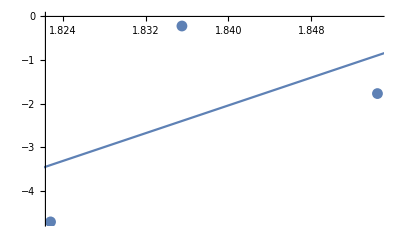

{0.18228,0.183554,0.18544,0.180871}

```mathematica
-148.78958843635712 + 79.75346478832577*x
```

```mathematica
Module[{parameters,parameterTableValues,rows,tableData,fits,digits},
digits=4;
fits=extBgFitsComplete;
parameters= ToString[#1[[1]],StandardForm]&/@(#1["BestFitParameters"])&/@fits;
parameters=MapThread[{ToString[Subscript[#1[[1]], #2],StandardForm],ToString[Subscript[#1[[2]], #2],StandardForm]}&,{parameters,Range[1,3]}]//Flatten;
parameterTableValues={ScientificForm[#1[[1]],digits],ScientificForm[#1[[2]],digits]}&/@#1["ParameterTableEntries"]&/@fits//Flatten[#,1]&;
rows=MapThread[Join[{#1},#2]&,{parameters,parameterTableValues}];
tableData=Join[{{"","Wert","Standardabweichung"}},rows];
Style[Grid[tableData,
Alignment->{Left,Automatic},Dividers->{{2->GrayLevel[0.7]},{2->GrayLevel[0.7]}},Spacings->{{2->1},{2->0.75}}],"DialogStyle"]
]
```

| Wert | Standardabweichung
"\!\(a\)"_1 | 1.815×10^-8 | 1.295×10^-7
"\!\(b\)"_1 | 4.132 | 1.343
"\!\(a\)"_2 | 1.436×10^-11 | 9.914×10^-10
"\!\(b\)"_2 | 4.966 | 1.299×10^1
"\!\(a\)"_3 | 9.655×10^-9 | 7.708×10^-7
"\!\(b\)"_3 | 3.655 | 1.503×10^1

### Abschwächung von Alpha-Strahlung in der Luft

{{1.42358,190.502},{2.26673,146.759},{2.94569,124.825},{3.54025,113.},{4.07761,101.944}}

{FittedModel[445.381 ⅇ^(-48.4417 (-0.947321+x)^2)],FittedModel[455.864 ⅇ^(-92.1242 (-1.89983+x)^2)],FittedModel[490.511 ⅇ^(-137.143 (-2.63363+x)^2)],FittedModel[482.02 ⅇ^(-186.679 (-3.25775+x)^2)],FittedModel[569.647 ⅇ^(-221.139 (-3.82276+x)^2)],FittedModel[520.702 ⅇ^(-228.326 (-4.33247+x)^2)]}

| Wert | Standardabweichung
μ | 9.473 | 9.171
σ | 1.016 | 9.171
k | 1.134 | 8.867 |  | Wert | Standardabweichung
μ | 1.9 | 7.209
σ | 7.367 | 7.209
k | 8.418 | 7.134 |  | Wert | Standardabweichung
μ | 2.634 | 5.945
σ | 6.038 | 5.945
k | 7.424 | 6.331
 | Wert | Standardabweichung
μ | 3.258 | 6.478
σ | 5.175 | 6.478
k | 6.253 | 6.779 |  | Wert | Standardabweichung
μ | 3.823 | 6.53
σ | 4.755 | 6.53
k | 6.79 | 8.076 |  | Wert | Standardabweichung
μ | 4.332 | 8.664
σ | 4.68 | 8.664
k | 6.108 | 9.794

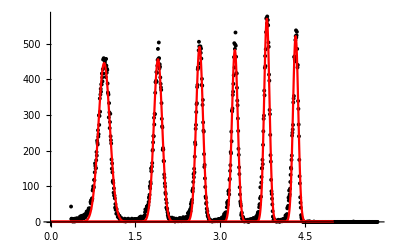

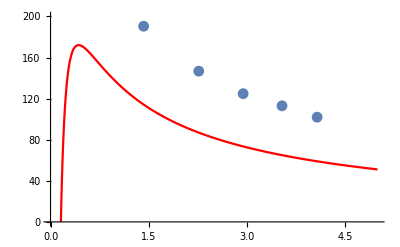

```mathematica
calibrAirData=MapIndexed[{(Normal[kalibrFunction]/.x->First[#2])/1000,#1}&,airData];
Export[Filepaths[[1]] <>"-calibrated.DAT", N[calibrAirData], "Table"];
Module[{parameters,intervals,fits,interval1,fit1,DiffValues,fitFunctions,values,gaussIntervals,theorie,e,z,Z,Wkin,me,i,mα,na,ϵ0,ρ,ML,A,u},
parameters={μ,σ,k};
intervals={{10,200},{200,350},{350,480},{480,600},{600,700},{700,800}};
fits=NonlinearModelFit[Take[calibrAirData,#1], model[x],parameters, x]&/@intervals;

interval1=Take[calibrAirData,intervals[[1]]];
fit1=NonlinearModelFit[interval1, model[x],parameters, x];


fitFunctions=#1["BestFit"]&/@fits;
(*Print[StringReplace[ToString[#1,InputForm]&/@fitFunctions,"E"->"e"]];*)
gaussIntervals=Quiet@Solve[#1==0.01,x]&/@fitFunctions;
gaussIntervals=gaussIntervals[[All,All,1,2]];
(*Print["domain="<>ToString[#1[[1]]]<>":"<>ToString[#1[[2]]]<>"]"&/@gaussIntervals];*)



e=1.6*10^(−19);
z=2;
Z=7.2;
mα=6.695*10^(−27);
me=9.1*10^-31;
na=6.02214*10^23;
i=86;
ϵ0=8.854187817*10^-12;
ρ=1.2928;
A=0.028964;
u=1.6605*10^-27;

values=#1["BestFitParameters"][[1,2]]&/@fits;
DiffValues={#1[[1]]+(#1[[2]]-#1[[1]])/2,(#1[[2]]-#1[[1]])/0.005}&/@Partition[values,2,1];
Print[DiffValues];
theorie[x_]=(e^4 mα z^2 Z ρ)/(8 A me π u x*10^6 ϵ0^2)*Log[(4 me x*10^6)/(i mα)]*1000*(10^6 e)^-2;

Print[fits];
Print[Grid[{{CustomParameterTable[fits[[1]],4],
CustomParameterTable[fits[[2]],4],
CustomParameterTable[fits[[3]],4]
},
{CustomParameterTable[fits[[4]],4],
CustomParameterTable[fits[[5]],4],
CustomParameterTable[fits[[6]],4]
}}]];


Export[Filepaths[[1]] <>"-dEdS.DAT", N[DiffValues], "Table"];


Print[Show[
ListPlot[calibrAirData,PlotStyle->Black],
Plot[fitFunctions,{x,0,5},PlotStyle->Red,PlotRange->All]
]];

Print[Show[
Plot[theorie[x],{x,0,5},PlotStyle->Red,PlotRange->{0,200}],
ListPlot[DiffValues,PlotRange->All]
]];
]
```